```mathematica
DV=3.166747
```

3.16675

```mathematica
3.166747
```

3.16675

```mathematica
SetDirectory["./"]
```

/home/users/alamman4/Desktop/Mathematicacoll

```mathematica
chr=OpenRead["POSCAR"];
dumiChar=Read[chr,Word]
dumInt=Read[chr,Number]

For[i=1,i≤3,
For[j=1,j≤3,
v[j,i]=Read[chr,Real];
j++];
i++];

dumiChar=Read[chr,Word];
dumiChar=Read[chr,Word];
dumiChar=Read[chr,Word];
numAtoms1=Read[chr,Number]
numAtoms2=Read[chr,Number];
numAtoms3=Read[chr,Number];
(*numAtoms4=Read[chr,Number];*)
numAtoms=numAtoms1+numAtoms2+numAtoms3;

dumiChar=Read[chr,Word]

For[i=1,i<=numAtoms,
x[i]={Read[chr,Real] ,Read[chr,Real],Read[chr,Real]};
i++];
Close[chr];
```

SrTiO3

1.

1

Direct

```mathematica
chr=OpenRead["EIGENVAL"];
dumInt=Read[chr,Number];
dumInt=Read[chr,Number];
dumInt=Read[chr,Number];
dumInt=Read[chr,Number];
dumReal=Read[chr,Real];
dumReal=Read[chr,Real];
dumReal=Read[chr,Real];
dumReal=Read[chr,Real];
dumReal=Read[chr,Real];
dumReal=Read[chr,Real];
dumiChar=Read[chr,Word];
dumiChar=Read[chr,Word];
(*minEnergy=Read[chr,Real];*)
totband=Read[chr,Number]
num=Read[chr,Number]
nPoints=Read[chr,Number]

For[j=1,j≤num,
kx=Read[chr,Real];
ky=Read[chr,Real];
kz=Read[chr,Real];
ddx=Read[chr,Real];
ll=Sqrt[kx*kx+ky*ky+kz*kz];
For[i=1,i<=nPoints,
bandtot[j,i]={ll,Read[chr,Real],Read[chr,Real]};
i++];
j++];
Close[chr];
```

40

30

24

```mathematica
For[ii=1,ii≤num,
band[ii]=Table[{bandtot[ii,j][[1]],bandtot[ii,j][[3]]},{j,1,nPoints}];
ii++]
```

```mathematica
bandtot[1,1][[3]]
```

-53.313

```mathematica
data1=Table[{x},{x,0,5}];
chen={"ka","ba"};
(*arrow ar prothom coordinate arrowar paca, second coor holo arrow head,text ar prothom coor holo position of text*)
```

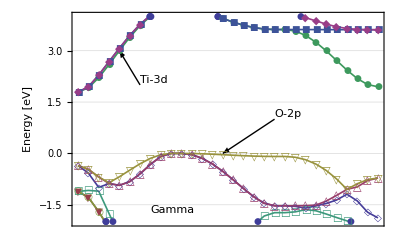

```mathematica
bal=ListPlot[Table[bandtot[j,i][[3]]-DV,{i,1,nPoints},{j,1,num}],PlotRange->{{1,30},{-2,4}},Joined->True,Frame->True,PlotStyle->Thickness[0.003],LabelStyle->Directive[Medium,FontFamily->"Helvetica"],GridLines->Automatic,PlotMarkers->{Automatic},FrameLabel->{"","Energy [eV]"},Frame->True,Axes->False,FrameTicks->{False,True}, Epilog->{{Arrow[{{20,1},{15,0}}],Text["O-2p",{20,1},{-1,-1}]},{Arrow[{{7,2},{5,3}}],Text["Ti-3d",{7,2},{-1,-1}]},{Text["Gamma",{8,-1.8},{-1,-1}]}}]
```

```mathematica
labels=Text[#[[1]],1.1 #[[{2,3}]]]&/@bal;
Show[bal]
```

Part::partw: Part {2, 3} of GraphicsComplex[{{1., -2.}, {30., -2.}, {1., -2.}, {30., -2.}, {1., -2.}, {30., -2.}, {1., -2.}, {30., -2.}, {1., -2.}, {30., -2.}, « 32 », {21., -1.73035}, {22., -1.7075}, {23., -1.64064}, {24., -1.67468}, {25., -1.77033}, {26., -1.87271}, {27., -1.9706}, {30., -2.}, « 164 »}, « 1 »] does not exist.

-Graphics-